```mathematica
points=ToExpression[Import["/home/tatjam/code/tfg/workdir/wing.dat","String"]];
```

```mathematica
normals=ToExpression[Import["/home/tatjam/code/tfg/workdir/wing_nrm.dat","String"]];
```

```mathematica
Graphics3D[{Thick,Red,Arrow[{{0,0,0},{0,0,1}}] (*Towards leading edge*),White, Polygon[points[[]]],Black,Arrowheads[Small],normals}]
```

-Graphics3D-

```mathematica
mat=Import["/home/tatjam/code/tfg/workdir/mat.dat"];
```

```mathematica
ArrayPlot[mat,PlotLegends->Automatic]
```

-Graphics-

```mathematica
dynmat=Import["/home/tatjam/code/tfg/workdir/dyn_mat.dat"];
```

```mathematica
ArrayPlot[dynmat,PlotLegends->Automatic]
```

-Graphics-

```mathematica
sln=Import["/home/tatjam/code/tfg/workdir/sln.dat"][[1]];
wake=ToExpression[Import["/home/tatjam/code/tfg/workdir/wake.dat","String"]];
wakesln=Import["/home/tatjam/code/tfg/workdir/wake_sln.dat"][[1]];
```

```mathematica
maxsol=Max[Abs[sln]];
```

```mathematica
If[maxsol==0,maxsol=0.0001];
```

```mathematica
maxwakesol=Max[Abs[wakesln]];
```

```mathematica
If[maxwakesol==0,maxwakesol=0.0001];
```

```mathematica
colorEach[p_,c_]:={FaceForm[ColorData["GrayYellowTones"][Abs[c/maxwakesol]]],Polygon[p]}
```

```mathematica
colorEachWake[p_,c_]:={FaceForm[ColorData["TemperatureMap"][Abs[c/maxwakesol]]],Polygon[p]}
```

```mathematica
Legended[Graphics3D[
ArrayFlatten[{EdgeForm[None],MapThread[colorEach,{points, sln}],MapThread[colorEachWake,{wake, wakesln}]},1],Lighting->{{"Ambient", White}}],{BarLegend[{"GrayYellowTones",{0,maxwakesol}}],BarLegend[{"TemperatureMap",{0,maxwakesol} }]}]
```

-Graphics3D-

```mathematica
cps=Import["/home/tatjam/code/tfg/workdir/cps.dat"][[1]];
```

```mathematica
maxcp=Max[cps]
```

3.0176

```mathematica
mincp=Min[cps]
```

0.00845117

```mathematica
If[maxcp==0,maxcp=0.0001];
```

```mathematica
colorEachCp[p_,c_]:={EdgeForm[None],FaceForm[ColorData["Rainbow"][(c-mincp)/(maxcp-mincp)]],Polygon[p]}
```

```mathematica
Legended[Graphics3D[
ArrayFlatten[{MapThread[colorEachCp,{points, cps}](*,Polygon[wake]*)},1],Lighting->{{"Ambient", White}}],BarLegend[{"Rainbow",{mincp,maxcp}}]]
```

-Graphics3D-

```mathematica
liftTime=Import["/home/tatjam/code/tfg/workdir/lift_over_time.dat"][[1]];
```

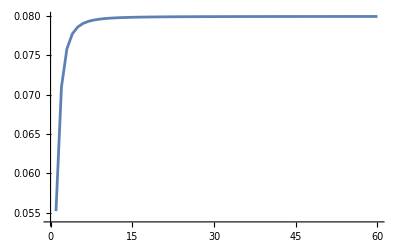

```mathematica
ListLinePlot[liftTime,PlotRange->All]
```